### Critically Damped Values: L=C, R=0.5; Underdamped Values= R = 500k, C = 6uF, L = 9nH; Overdamped Values = R = 0.3, C = L = 1;

ζ= 1.66667 > 1 → overdamped

V_c(t) = 3. ⅇ^(-3.33333 t) (-0.666667 ⅇ^(0.333333 t)+1. ⅇ^(3. t))

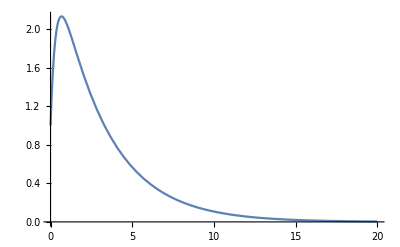

i_c(t) = -10. ⅇ^(-3.33333 t) (-0.666667 ⅇ^(0.333333 t)+1. ⅇ^(3. t))+3. ⅇ^(-3.33333 t) (-0.222222 ⅇ^(0.333333 t)+3. ⅇ^(3. t))

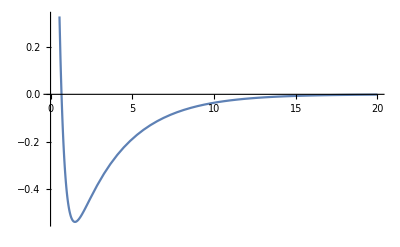

i_L(t) = 0.666667 ⅇ^(-3. t)-9. ⅇ^(-0.333333 t)

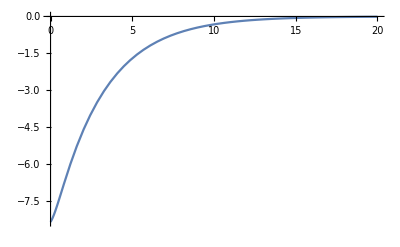

i_R(t) = 10. ⅇ^(-3.33333 t) (-0.666667 ⅇ^(0.333333 t)+1. ⅇ^(3. t))

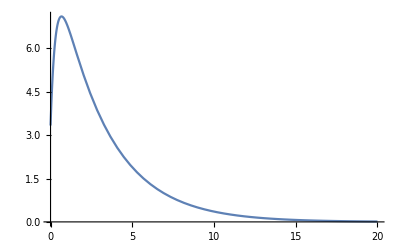

```mathematica
(*This Program gets the natural response of a simple parallel RLC circuit with no external source*)
Clear["Global`*"]
R = 0.3(*Input["Enter The Value Of Resistance"]*);
Capacitor=1(*Input["Enter The Value Of Capacitance"]*);
L= 1(*Input["Enter The Value Of L"]*);
(*test*)
ωc=√(1/(L Capacitor));
ζ = 1/(2 ωc R Capacitor);
eqn1=V''[t]+2 ζ ωc V'[t]+ωc^2 V[t]==0;
capVoltage = DSolve[{eqn1, V[0]==1, V'[0]==5},V[t],t][[1]];
Vc[t_]:=V[t]/.capVoltage
inductorCurrent=1/L∫Vc[t]ⅆt;
If[ζ<1,output=StringForm["ζ= `` < 1 → underdamped", ζ], If[ζ>1, output=StringForm["ζ= `` > 1 → overdamped", ζ], output=StringForm["ζ=1 →  critically damped", ζ]]];
Style[output,Blue,18]
Style[StringForm["V_c(t) = ``", Vc[t]], Blue, 18]

Plot[Vc[t],{t,0,20}, PlotRange->Automatic]
CapacitorCurrent=Capacitor D[Vc[t],t];
ic[t_]:=CapacitorCurrent;
Style[StringForm["i_c(t) = ``", ic[t]], Blue, 18]
Plot[ic[t],{t,0,20}]
i[t_]:=inductorCurrent;
Style[StringForm["i_L(t) = ``",i[t]], Blue, 18]
Plot[i[t],{t,0,20}]
ResistorCurrent=1/R Vc[t];
iR[t_]:=ResistorCurrent;
Style[StringForm["i_R(t) = ``", iR[t]], Blue, 18]
Plot[iR[t],{t,0,20}]
```

ζ= 0.9 < 1 → underdamped

i_L(t) = 1. ⅇ^(-9. t) (1. Cos[4.3589 t]+0.688247 Sin[4.3589 t])

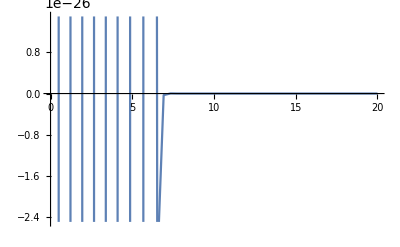

V_L(t) = 0.5 (1. ⅇ^(-9. t) (3. Cos[4.3589 t]-4.3589 Sin[4.3589 t])-9. ⅇ^(-9. t) (1. Cos[4.3589 t]+0.688247 Sin[4.3589 t]))

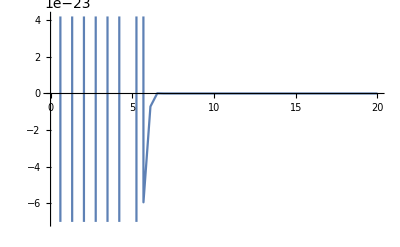

V_R(t) = 9. ⅇ^(-9. t) (1. Cos[4.3589 t]+0.688247 Sin[4.3589 t])

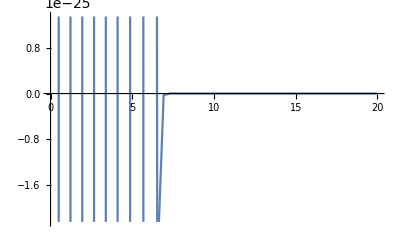

V_c(t) = 0.02 (1. ⅇ^(-9. t) (3. Cos[4.3589 t]-4.3589 Sin[4.3589 t])-9. ⅇ^(-9. t) (1. Cos[4.3589 t]+0.688247 Sin[4.3589 t]))

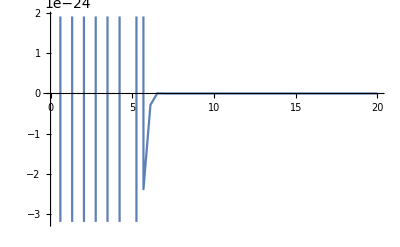

```mathematica
Clear["Global`*"]

(*This Program outputs the natural response of a series RLC circuit*)


R = 9(*Input["Enter The Value Of Resistance"]*);
Capacitor=0.02(*Input["Enter The Value Of Capacitance"]*);
L= 0.5(*Input["Enter The Value Of L"]*);
ω= 1/(√(L Capacitor));
ζ=R/(2 ω L);
eqn2 =r''[t]+2 ζ ω r'[t]+ω^2 r[t]==0;
inductorCurrent = DSolve[{eqn2,r[0]==1,r'[0]==-6},r[t],t][[1]];
iL[t_]:=r[t]/.inductorCurrent;
If[ζ<1,output=StringForm["ζ= `` < 1 → underdamped", ζ], If[ζ>1, output=StringForm["ζ= `` > 1 → overdamped", ζ], output=StringForm["ζ=1 →  critically damped", ζ]]];
Style[output,Blue,18]
Style[StringForm["i_L(t) = ``", iL[t]], Blue, 18]
Plot[iL[t],{t,0,20}]
ResistorVoltage = R*iL[t];
inductorVoltage = L D[iL[t],t];
VL[t_]:=inductorVoltage;
Style[StringForm["V_L(t) = ``", VL[t]], Blue, 18]
Plot[VL[t],{t,0,20}]
VR[t_]:=ResistorVoltage;
Style[StringForm["V_R(t) = ``", VR[t]], Blue, 18]
Plot[VR[t],{t,0,20}]
CapVoltage = Capacitor D[iL[t],t];
Vc[t_]:=CapVoltage;
Style[StringForm["V_c(t) = ``", Vc[t]], Blue, 18]
Plot[Vc[t],{t,0,20}]
```